# Multi-time correlation analysis of return moments

## Initialization and options

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{NotebookDirectory[],"Packages","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{NotebookDirectory[],"Packages","EconomicComputations.wl"}]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
```

```mathematica
ReturnMeans[returnsVsLag_]:=Map[{First[#[[All,1]]],Mean[#[[All,2]]]}&,GatherBy[returnsVsLag,First]];
```

## Load database

```mathematica
path = FileNameJoin[{NotebookDirectory[],"DJI_DAX_MXX_NIKKEI_dataset.mx"}];
database = Import[path];
```

## Distribución retornos 3D

```mathematica
Plot3DDist[market_]:=Block[{returnsVsLag,means},
returnsVsLag = MultiscaleReturns[market["Prices"],Length[market["Prices"]]-1];
means = ReturnMeans[returnsVsLag];

Show[
DensityHistogram[
returnsVsLag,
Automatic,
"Probability",
ImageSize->plotSize,
PlotTheme->"Monochrome",
FrameLabel->{Style["Lag",bigFontSize],Style["Return",bigFontSize]},
Frame->True,BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
ChartLegends->Automatic,
ColorFunction->"SolarColors",
PlotLabel->market["Name"]
],
ListLinePlot[means,PlotStyle->Black,PlotLegends->Placed[{"Media"},{Right,Top}]]
]
];
```

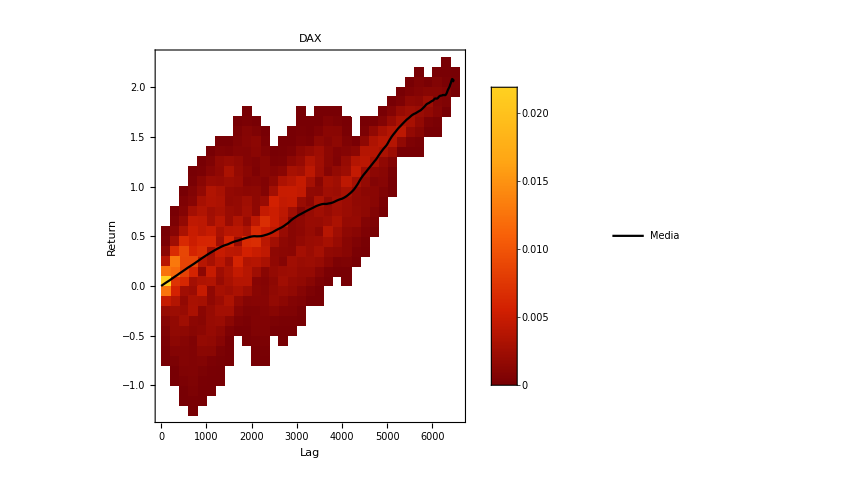
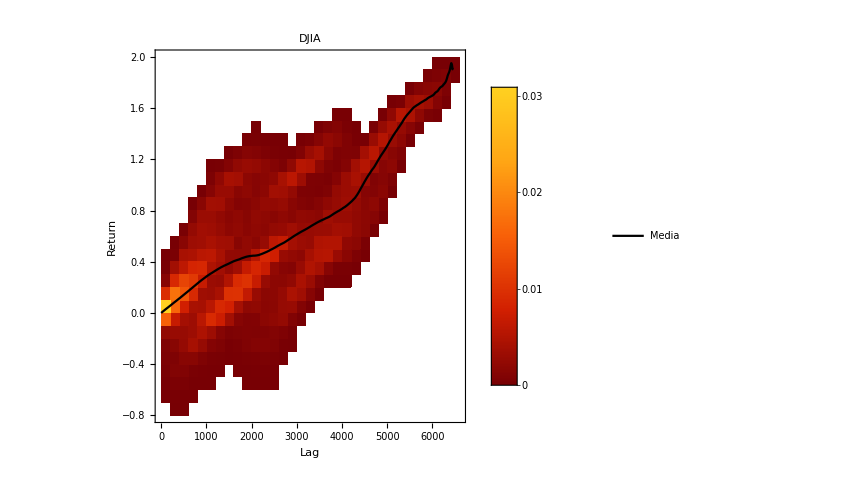
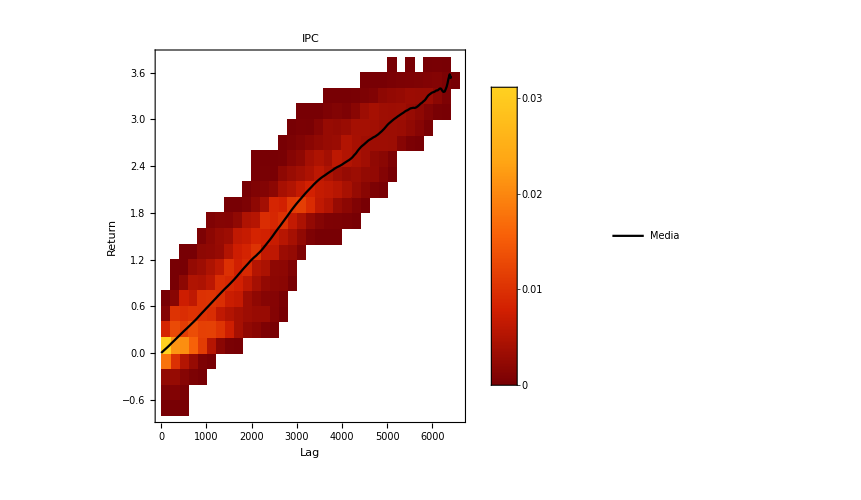
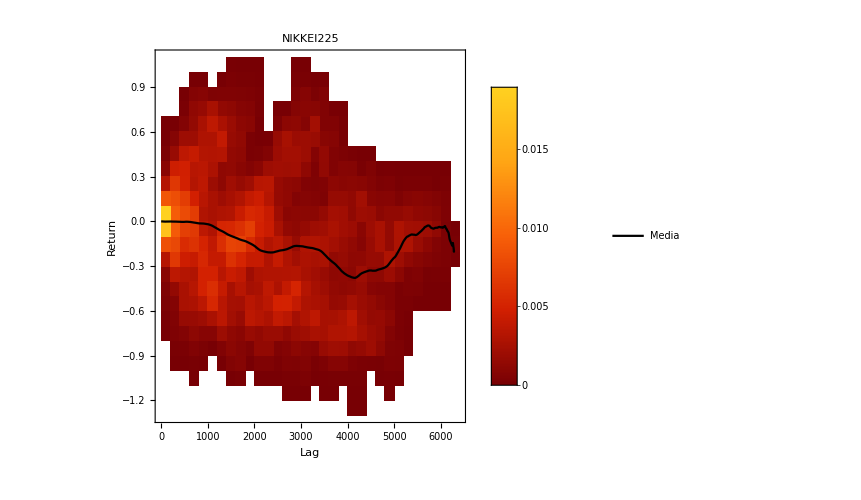

```mathematica
ProgressMap[Plot3DDist,database]
```

## Trendless

```mathematica
Plot3DDetrended[market_]:=Block[{returnsVsLag,means},
returnsVsLag = DetendedMultiscaleReturns[market["Prices"],Length[market["Prices"]]-1];
means = ReturnMeans[returnsVsLag];

Show[
DensityHistogram[
returnsVsLag,
Automatic,
"Probability",
ImageSize->plotSize,
PlotTheme->"Monochrome",
FrameLabel->{Style["Lag",bigFontSize],Style["Return",bigFontSize]},
Frame->True,BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
ChartLegends->Automatic,
ColorFunction->"SolarColors",
PlotLabel->market["Name"],
PerformanceGoal->"Speed"
],
ListLinePlot[means,PlotStyle->Black,PlotLegends->Placed[{"Media"},{Right,Top}]]
]
];
```

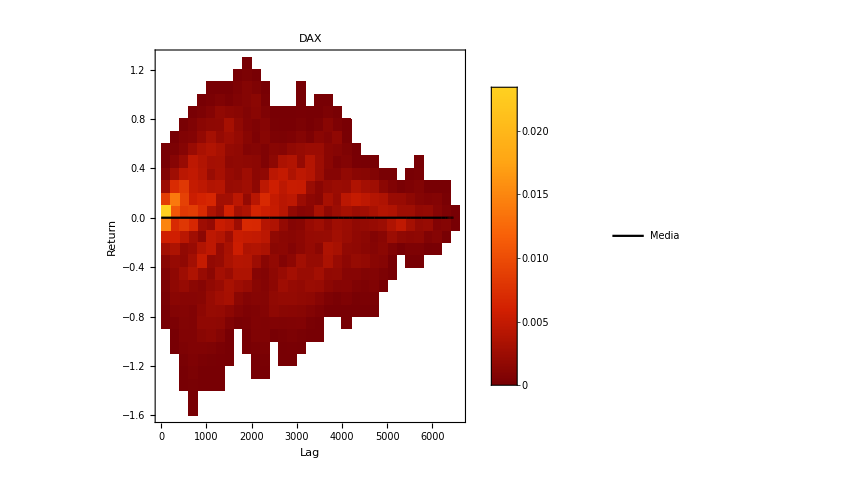
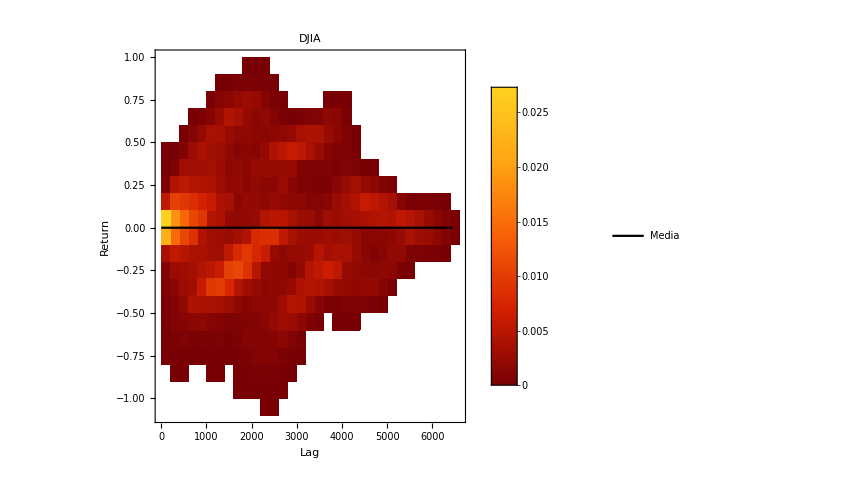
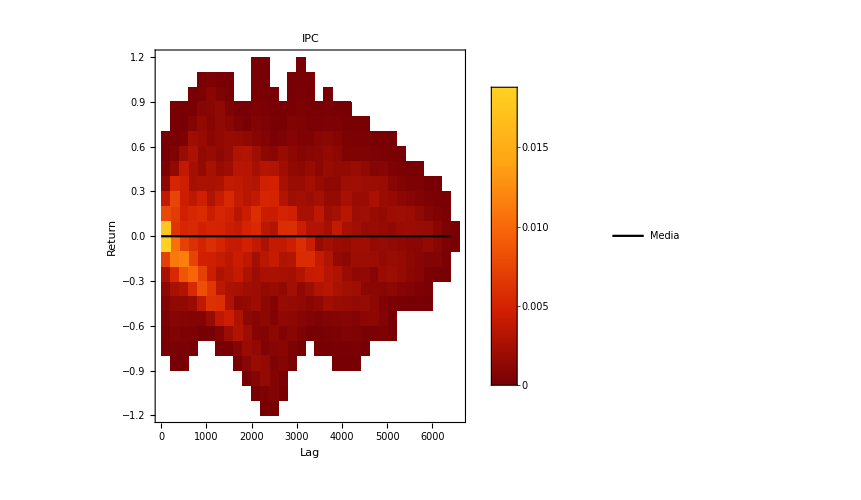
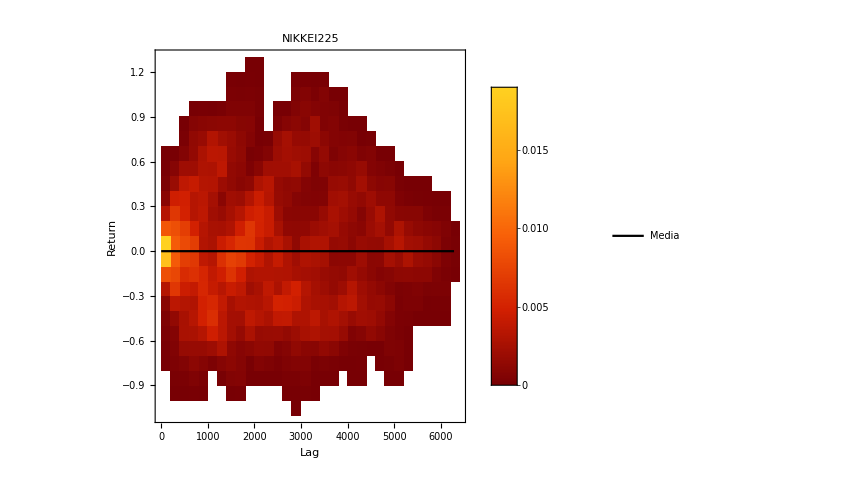

```mathematica
ProgressMap[Plot3DDetrended,database]
```

Simetría

```mathematica
DetendedMultiscaleReturnsSymmetry[prices_,maxLag_,skip_:5]:= Block[{ret},
ret = GatherBy[DetendedMultiscaleReturns[prices,maxLag,skip],First];
ret = Map[{#[[1,1]],Tn[#[[All,2]]]}&,ret];
Return[ret];
];

PlotSimm[market_,skip_:5]:=Block[{tnVsLag,upp1,upp2,upp3},
tnVsLag = DetendedMultiscaleReturnsSymmetry[market["Prices"],Length[market["Prices"]]-1,skip];

upp1 = {{1, UpperPercentagePoint[0.01]},{Floor[Length[market["Prices"]]-1],UpperPercentagePoint[0.01]}};
upp2 = {{1, UpperPercentagePoint[0.05]},{Floor[Length[market["Prices"]]-1],UpperPercentagePoint[0.05]}};
upp3 = {{1, UpperPercentagePoint[0.1]},{Floor[Length[market["Prices"]]-1],UpperPercentagePoint[0.1]}};

ListLinePlot[
{tnVsLag,upp1,upp2,upp3},
ImageSize->plotSize,
PlotTheme->"Monochrome",
FrameLabel->{Style["Lag",bigFontSize],Style["T_n",bigFontSize]},
Frame->True,BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotMarkers->None, 
PlotStyle->colors,
PlotLegends->Placed[{"T_n","99% CL","95% CL","90% CL"},{Right,Top}],
PlotLabel->market["Name"]
]

];
```

```mathematica
ProgressMap[PlotSimm,database]
```

$Aborted

```mathematica
WhenSimm[market_]:=Block[{tnVsLag,uppL,selected},
uppL = UpperPercentagePoint[0.01];
tnVsLag = DetendedMultiscaleReturnsSymmetry[market["Prices"],Length[market["Prices"]]-1];
selected = Select[tnVsLag,Last[#]<uppL&];
Return[selected];
];
```

```mathematica
whenSimm = Map[WhenSimm,database];
```

```mathematica
Grid[MapThread[{#1["Name"],#2[[All,1]]}&,{database,whenSimm}]]
```

Skewness

```mathematica
DetendedMultiscaleReturnsSkewness[prices_,maxLag_,skip_:5]:= Block[{ret},
ret = GatherBy[DetendedMultiscaleReturns[prices,maxLag-1,skip],First];
ret = Map[{#[[1,1]],Skewness[#[[All,2]]]}&,ret];
Return[ret];
];

PlotSkewness[market_]:=Block[{skwVsLag,upp1,upp2,upp3},
skwVsLag = DetendedMultiscaleReturnsSkewness[market["Prices"],Length[market["Prices"]]-1];

ListLinePlot[
skwVsLag,
ImageSize->plotSize,
PlotTheme->"Monochrome",
FrameLabel->{Style["Lag",bigFontSize],Style["T_n",bigFontSize]},
Frame->True,BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotMarkers->None, 
PlotStyle->colors,
PlotLegends->Placed[{"T_n","99% CL","95% CL","90% CL"},{Right,Top}],
PlotLabel->market["Name"],
PlotRange->All
]

];
```

```mathematica
ProgressMap[PlotSkewness,database]
```

- Utilizar la dist “total” y ver si es simétria
- Comparar con los retornos indep
- También checar el cuarto momento

Distribución total

### Standard

```mathematica
PlotTotalDist[market_]:=Block[{totalDist},
totalDist= MultiscaleReturns[market["Prices"],Length[market["Prices"]]-1];

SmoothHistogram[
totalDist,
ImageSize->plotSize,
PlotTheme->"Monochrome",
FrameLabel->{Style["Return",bigFontSize],Style["PDF",bigFontSize]},
Frame->True,BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotLabel->market["Name"]
]

];
```

```mathematica
Map[PlotTotalDist,database]
```

$Aborted

### Detrended

```mathematica
PlotTotalDist[market_]:=Block[{totalDist},
totalDist= DetendedMultiscaleReturns[market["Prices"],Length[market["Prices"]]-1];

SmoothHistogram[
totalDist,
ImageSize->plotSize,
PlotTheme->"Monochrome",
FrameLabel->{Style["Return",bigFontSize],Style["PDF",bigFontSize]},
Frame->True,BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotLabel->market["Name"]
]

];
```

```mathematica
Map[PlotTotalDist,database]
```

## Uncorrelated

```mathematica
Means[returnsVsLag_]:=Map[{First[#[[All,1]]],Mean[#[[All,2]]]}&,GatherBy[returnsVsLag,First]];
Plot3DDistUncorrelated[market_]:=Block[{returnsVsLag,means},
returnsVsLag = UncorrelatedMultiscaleReturns[market["Prices"],Length[market["Prices"]]-1];
means = ReturnMeans[returnsVsLag];

Show[
DensityHistogram[
returnsVsLag,
Automatic,
"Probability",
ImageSize->plotSize,
PlotTheme->"Monochrome",
FrameLabel->{Style["Lag",bigFontSize],Style["Return",bigFontSize]},
Frame->True,BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
ChartLegends->Automatic,
ColorFunction->"SolarColors",
PlotLabel->market["Name"]
],
ListLinePlot[means,PlotStyle->Black,PlotLegends->Placed[{"Media"},{Right,Top}]]
]
];
```

```mathematica
Map[Plot3DDistUncorrelated,database]
```

Skewness y T_n

```mathematica
SkwReturnsVsLag[prices_,maxLag_]:= Table[{Δt,Skewness[Returns[prices,Δt]]},{Δt,1,maxLag-2}];

SkwUncorrelatedReturnsVsLag[prices_,maxLag_]:=Table[{Δt,Skewness[UncorrelatedReturns[prices,Δt]]},{Δt,1,maxLag-2}];

TnReturnsVsLag[prices_,maxLag_]:= Table[{Δt,Skewness[Returns[prices,Δt]]},{Δt,1,maxLag-2}];

TnUncorrelatedReturnsVsLag[prices_,maxLag_]:= Table[{Δt,Skewness[UncorrelatedReturns[prices,Δt]]},{Δt,1,maxLag-2}];

Plot3DSimmSkw[market_]:=Block[{corr,uncorr},
corr = SkwReturnsVsLag[market["Prices"],Length[market["Prices"]]-1];
uncorr = SkwUncorrelatedReturnsVsLag[market["Prices"],Length[market["Prices"]]-1];

ListLinePlot[
{corr,uncorr},
ImageSize->plotSize,
PlotRange->Full,
PlotTheme->"Monochrome",
FrameLabel->{Style["Lag",bigFontSize],Style["Skewness",bigFontSize]},
Frame->True,BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotLegends->{"Uncorrelated", "Correlated"},
PlotLabel->market["Name"],
PlotStyle->colors
]
];
```

```mathematica
Plot3DSimmSkw[market]
```